```mathematica
Gam[x_,y_]:=-Series[(1-I*(-1-Cos[x]-Cos[y]+(1/4)Cos[2y]-(1/6)Sin[x]Sin[2x])),{x,0,6},{y,0,8}]
```

```mathematica
Gam[x,y]//ExpandAll
```

(-(1+(11 ⅈ)/4)+(ⅈ y^4)/8-(ⅈ y^6)/48+(ⅈ y^8)/640+O[y]^9)+(ⅈ x^2)/6+(17 ⅈ x^4)/72-(179 ⅈ x^6)/2160+O[x]^7

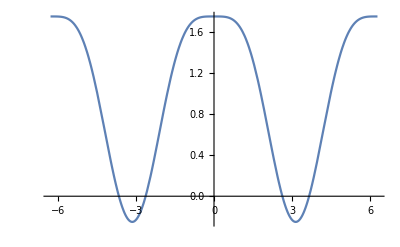

```mathematica
Plot[1+Cos[y]-(1/4)Cos[2y],{y,-2Pi,2Pi}]
```

Note that PhiHat[x,y] must look something like 1 + iP([x,y]) where P is positive homogeneous.

```mathematica
Plot3D[Abs[2+I*(-2-Cos[x]-Cos[y]+(1/4)Cos[2y])],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
RulePhi={Cos[x]->(1/2)(E^(I*x)+E^(-I*x)),
Cos[2x]->(1/2)(E^(2I*x)+E^(-2I*x)),
Cos[y]->(1/2)(E^(I*y)+E^(-I*y)),
Cos[2y]->(1/2)(E^(2I*y)+E^(-2I*y))};
```

```mathematica
PhiHat[x_,y_]:=(1-I*(-1+11/4-Cos[x]-Cos[y]+(1/4)Cos[2y]-(1/6)Sin[x]Sin[2x]))
```

```mathematica
PhiHat[0,0]
```

1

```mathematica
Series[Log[PhiHat[x,y]/PhiHat[0,0]],{x,0,4},{y,0,6}]
```

((ⅈ y^4)/8-(ⅈ y^6)/48+O[y]^7)+((5 ⅈ)/2+(5 y^4)/16-(5 y^6)/96+O[y]^7) x^2+((25/8-(41 ⅈ)/24)-(41/192+(25 ⅈ)/32) y^4+(41/1152+(25 ⅈ)/192) y^6+O[y]^7) x^4+O[x]^5

```mathematica
Plot3D[Abs[(1+I*(0.5+(3/4)Cos[x]-Cos[y]+(1/4)Cos[2y]))],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
PhiHat[0,0]
```

(4-11 ⅈ)/(√137)

```mathematica
PhiHatNew[x_,y_]:=PhiHat[x,y]/PhiHat[0,0];
```

```mathematica
Plot3D[Abs[PhiHat[x,y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
Series[Log[PhiHatNew[x,y]],{x,0,3},{y,0,6}]//Simplify
```

(-(11/274-(2 ⅈ)/137) y^4+(11/1644-ⅈ/411) y^6+O[y]^7)+(-(22/137-(8 ⅈ)/137)-(105/18769-(88 ⅈ)/18769) y^4+(35/37538-(44 ⅈ)/56307) y^6+O[y]^7) x^2+O[x]^4

Note that we must normalize by a real number so as not to introduce “real impurities”

```mathematica
Abs[PhiHat[0,0]]
```

1

```mathematica
PhiHat[x,y]/.RulePhi//ExpandAll
```

(1+(7 ⅈ)/4)-1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-ⅈ y)-1/2 ⅈ ⅇ^(ⅈ y)+1/8 ⅈ ⅇ^(-2 ⅈ y)+1/8 ⅈ ⅇ^(2 ⅈ y)

```mathematica
PhiHat[0,0]
```

1

```mathematica
(1+(7 ⅈ)/4)-1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-ⅈ y)-1/2 ⅈ ⅇ^(ⅈ y)+1/8 ⅈ ⅇ^(-2 ⅈ y)+1/8 ⅈ ⅇ^(2 ⅈ y)
```

(1+(7 ⅈ)/4)-1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)-1/2 ⅈ ⅇ^(-ⅈ y)-1/2 ⅈ ⅇ^(ⅈ y)+1/8 ⅈ ⅇ^(-2 ⅈ y)+1/8 ⅈ ⅇ^(2 ⅈ y)

```mathematica
Series[Log[PhiHat[x,y]],{x,0,4},{y,0,6}]
```

((ⅈ y^4)/8-(ⅈ y^6)/48+O[y]^7)+(ⅈ/2+y^4/16-y^6/96+O[y]^7) x^2+((1/8-ⅈ/24)-(1/192+ⅈ/32) y^4+(1/1152+ⅈ/192) y^6+O[y]^7) x^4+O[x]^5

```mathematica
FourierSeries[E^(I*(x^2+y^4)),{x,y},{2,4}]
```

$Aborted

Let us try again...

```mathematica
Lg[x,y]:=Series[2-(I/2)*Sin[x]^2-Sin[x]^4 -(I/2)*Sin[y]^4-Sin[y]^8,{x,0,6},{y,0,8}]
```

```mathematica
Lg[x,y]
```

(2-(ⅈ y^4)/2+(ⅈ y^6)/3-(1+ⅈ/10) y^8+O[y]^9)-(ⅈ x^2)/2-(1-ⅈ/6) x^4+(2/3-ⅈ/45) x^6+O[x]^7

```mathematica
PhiH[x_,y_]:=(2-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8)/2
```

```mathematica
PhiH[x,y]
```

1/2 (2-1/2 ⅈ Sin[x/2]^2-Sin[x/2]^4-1/2 ⅈ Sin[y/2]^4-Sin[y/2]^8)

```mathematica
PhiH[0,0]
```

1

```mathematica
Series[Log[PhiH[x,y]/PhiH[0,0]],{x,0,4},{y,0,6}]
```

(-(ⅈ y^4)/64+(ⅈ y^6)/384+O[y]^7)+(-ⅈ/16+y^4/1024-y^6/6144+O[y]^7) x^2+(-(15/512-ⅈ/192)-(1/12288+(7 ⅈ)/16384) y^4+(1/73728+(7 ⅈ)/98304) y^6+O[y]^7) x^4+O[x]^5

```mathematica
Plot3D[Abs[PhiH[x,y]],{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-

```mathematica
RulePhi={Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2))};
```

```mathematica
PhiH[x,y]/.RulePhi//ExpandAll
```

(173/256-(7 ⅈ)/32)+(1/8+ⅈ/16) ⅇ^(-ⅈ x)+(1/8+ⅈ/16) ⅇ^(ⅈ x)-1/32 ⅇ^(-2 ⅈ x)-1/32 ⅇ^(2 ⅈ x)+(7/64+ⅈ/16) ⅇ^(-ⅈ y)+(7/64+ⅈ/16) ⅇ^(ⅈ y)-(7/128+ⅈ/64) ⅇ^(-2 ⅈ y)-(7/128+ⅈ/64) ⅇ^(2 ⅈ y)+1/64 ⅇ^(-3 ⅈ y)+1/64 ⅇ^(3 ⅈ y)-1/512 ⅇ^(-4 ⅈ y)-1/512 ⅇ^(4 ⅈ y)

```mathematica
PhiHCx[x_,y_]:=(6-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8-(I/2)*Sin[x]Cos[y]-(1/2)Sin[x]^2Cos[y])/3
```

```mathematica
Series[PhiHCx[x,y],{x,0,4},{y,0,6}]
```

(2-(ⅈ y^4)/96+(ⅈ y^6)/576+O[y]^7)+(-ⅈ/6+(ⅈ y^2)/12-(ⅈ y^4)/144+(ⅈ y^6)/4320+O[y]^7) x+(-(1/6+ⅈ/24)+y^2/12-y^4/144+y^6/4320+O[y]^7) x^2+(ⅈ/36-(ⅈ y^2)/72+(ⅈ y^4)/864-(ⅈ y^6)/25920+O[y]^7) x^3+((5/144+ⅈ/288)-y^2/36+y^4/432-y^6/12960+O[y]^7) x^4+O[x]^5

```mathematica
PhiHCx[0,0]
```

2

```mathematica
FindMaximum[Abs[PhiHCx[x,y]],{x,-2},{y,6}]
```

{2.,{x→6.78916×10^-7,y→6.15454}}

```mathematica
Plot3D[Abs[PhiHCx[x,y]],{x,-3Pi,3Pi},{y,-3Pi,3Pi}]
```

-Graphics3D-

```mathematica
RulePhiCx={Sin[x/2]->(1/(2I))(E^(I*x/2)-E^(-I*x/2)),
Sin[y/2]-> (1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]Sin[y/2]^2-> (1/(2I))(E^(I*x)-E^(-I*x))(1/(2I))(E^(I*y/2)-E^(-I*y/2))(1/(2I))(E^(I*y/2)-E^(-I*y/2)),
Sin[x]->(1/(2I))(E^(I*x)-E^(-I*x)),
Sin[y]-> (1/(2I))(E^(I*y)-E^(-I*y))};
```

```mathematica
PhiHCx[x,y]/.RulePhiCx//ExpandAll
```

(301/384-(7 ⅈ)/48)+(1/24+ⅈ/24) ⅇ^(-ⅈ x)+(1/8+ⅈ/24) ⅇ^(ⅈ x)-1/48 ⅇ^(-2 ⅈ x)-1/48 ⅇ^(2 ⅈ x)+1/48 ⅇ^(-ⅈ x-2 ⅈ y)-1/48 ⅇ^(ⅈ x-2 ⅈ y)+1/48 ⅇ^(-ⅈ x+2 ⅈ y)-1/48 ⅇ^(ⅈ x+2 ⅈ y)+(7/96+ⅈ/24) ⅇ^(-ⅈ y)+(7/96+ⅈ/24) ⅇ^(ⅈ y)-(7/192+ⅈ/96) ⅇ^(-2 ⅈ y)-(7/192+ⅈ/96) ⅇ^(2 ⅈ y)+1/96 ⅇ^(-3 ⅈ y)+1/96 ⅇ^(3 ⅈ y)-1/768 ⅇ^(-4 ⅈ y)-1/768 ⅇ^(4 ⅈ y)

```mathematica
(6-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8-(I/2)*Sin[x]Cos[y]-(1/2)Sin[x]^2Cos[y])(6-(I/2)*Sin[x/2]^2-Sin[x/2]^4 -(I/2)*Sin[y/2]^4-Sin[y/2]^8-(I/2)*Sin[x]Cos[y]-(1/2)Sin[x]^2Cos[y])
```